```mathematica
FileExport[data_, filename_?StringQ] :=
With[
{folder=FileNameJoin[{NotebookDirectory[], "pic"}]},
If[FileType[folder]== None,CreateDirectory[folder]];
Export[FileNameJoin[{folder,StringJoin[filename, ".pdf"]}] , data, "PDF"];
];
```

```mathematica
(* 
1 - коллокация в точке;
2 - коллокация в подобластях;
3 - метод Бубнова - Галеркина;
4 - метод Галеркина;
5 - МНК; 
6 - метод Ритца;
*)
nM =1; (* номер метода *)
p = 8; (* порядок *)
```

## Исходные данные

```mathematica
leftBond=0;
rightBond=1;
A[ϕ_,x_]:=D[ϕ,{x,2}]+ϕ;
F[x_]:=-x;
ϕi[x_,i_]:=x^i-x^(i+1);
```

## Функции

```mathematica
projectionMethod[methodNumber_,order_]:=Module[{a,u,ψ,eq,eqRight,solA,numSol},
a=Table[Subscript[aa, i],{i,1,order}];

u=a.Table[ϕi[x,i],{i,1,order}];
Switch[methodNumber,
1,ψ=Table[DiracDelta[x-(leftBond + i (rightBond-leftBond)/(order+1))],{i,1,order}],
2,ψ=Table[If[leftBond+(i-1)(rightBond-leftBond)/order≤x<leftBond+i(rightBond-leftBond)/order,1,0],{i,1,order}],
3,ψ=Table[ϕi[x,i],{i,1,order}],
4,ψ=Table[(x-1/2)^(i-1),{i,1,order}],
5,ψ=Table[A[ϕi[x,i],x],{i,1,order}],
6,ψ=Table[D[u,Subscript[aa, i]],{i,1,order}]
];
eq=Table[∑_(i=1)^order a⟦i⟧∫_leftBond^rightBond A[ϕi[x,i],x]ψ⟦j⟧ⅆx,{j,1,order}];
eqRight=Table[∫_leftBond^rightBond F[x]ψ⟦j⟧ⅆx,{j,1,order}];
solA=Solve[eq==eqRight,a]⟦1⟧;
numSol[x_]:=∑_(i=1)^order a⟦i⟧ϕi[x,i]/.solA;
{a/.solA,numSol[x]}
]
```

```mathematica
makePrint[methodNumber_,quantity_]:=Module[{analyticalSol,i,a,numSol,δ,tableFraction,tableNum,tableErr,plot,errPlot,name},
analyticalSol[x]:=DSolve[{A[u[ξ],ξ]==F[ξ],u[leftBond]==0,u[rightBond]==0},u[ξ],ξ]⟦1,1,2⟧/.ξ->x;
result={};
For[i=1,i≤quantity,i++,
{a,numSol[x]}=projectionMethod[methodNumber,i];
δ=√(Integrate[(analyticalSol[x]-numSol[x])^2,{x,leftBond,rightBond}]/Integrate[(analyticalSol[x])^2,{x,leftBond,rightBond}])//N;
result=Append[result,{a,numSol[x],δ}];
];
(*solsForPlot=Append[result⟦;;,2⟧,analyticalSol[x]];*)
solsForPlot=result⟦1;;Min[3,Length[result]],2⟧;
(*Print[result⟦;;,2⟧];*)
solsForPlot=Append[solsForPlot,analyticalSol[x]];
tableFraction = Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],result⟦;;,1⟧},{"N","a_i"}],Frame->All];
tableNum =Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],N[result⟦;;,1⟧]},{"N","a_i//N"}],Frame->All];
tableErr=Grid[Prepend[Transpose@{Table[i,{i,1,quantity}],result⟦;;,3⟧},{"N","δ"}],Frame->All];
plot=Plot[solsForPlot,{x,leftBond,rightBond},PlotLegends->Append[Table["N = "<>ToString[i],{i,1,Min[quantity,3]}],"Analytical"],AxesStyle->Black,LabelStyle->{13,Black},AxesLabel->{"x","u(x)"},PlotRange->All, ImageSize->700, PlotStyle->{Red, Blue, Green, {Black, Dashed}}];
errPlot = ListPlot[result⟦;;,3⟧, Ticks->{Table[i, {i, 1, quantity}], Automatic}];
Return[{tableFraction, tableNum, tableErr, plot, errPlot}];
]
```

## Печать результатов

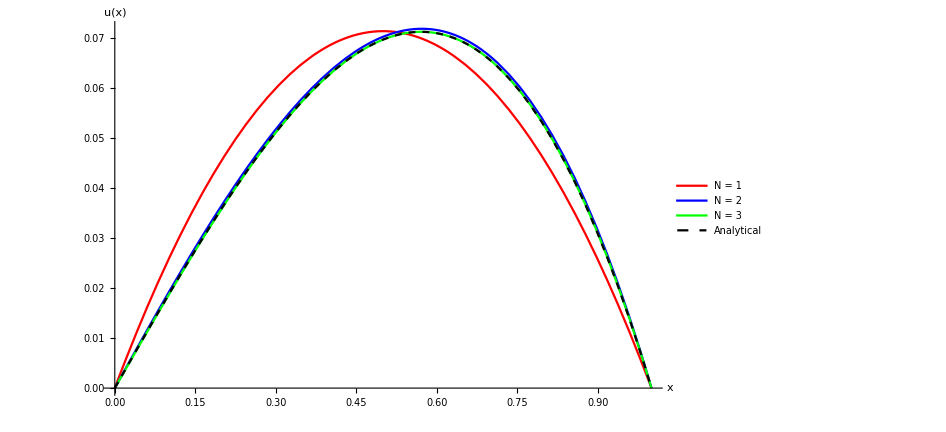
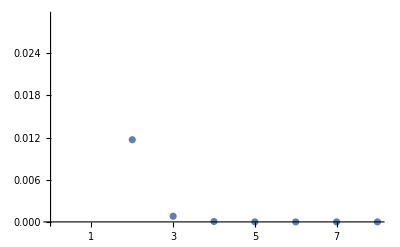
{N | a_i
1 | {2/7}
2 | {81/416,9/52}
3 | {4714/25203,24656/126015,-32/1355}
4 | {45172500/239841269,45261000/239841269,-5070625/479682538,-625/72274}
5 | {2909275309/15441853760,363525003/1930231720,-18172467/1930231720,-4925043/482557930,81/102836}
6 | {19336904280547/102640059933458,251376964566931/1334320779134954,-25781565304775/2668641558269908,-51758232400105/5337283116539816,181129812122/667160389567477,117649/570973544}
7 | {558519214931800882/2964616653838951727,558519973325839312/2964616653838951727,-28674598603125408/2964616653838951727,-28653410716928000/2964616653838951727,653331183742976/2964616653838951727,735459422568448/2964616653838951727,-131072/9312036547}
8 | {4749734557488858228/25211560287685034519,52247081773221453288/277327163164535379709,-2681972031025139337/277327163164535379709,-42910540607055008997/4437234610632566075344,2059299731056045239/8874469221265132150688,2071054129606072659/8874469221265132150688,-35875298807046099/8874469221265132150688,-4782969/1670226853408},N | a_i//N
1 | {0.285714}
2 | {0.194712,0.173077}
3 | {0.187041,0.195659,-0.0236162}
4 | {0.188343,0.188712,-0.0105708,-0.00864765}
5 | {0.188402,0.188332,-0.00941466,-0.0102061,0.000787662}
6 | {0.188395,0.188393,-0.00966093,-0.00969749,0.000271494,0.00020605}
7 | {0.188395,0.188395,-0.00967228,-0.00966513,0.000220376,0.000248079,-0.0000140755}
8 | {0.188395,0.188395,-0.00967079,-0.00967056,0.000232048,0.000233372,-4.04253×10^-6,-2.86366×10^-6},N | δ
1 | 0.118538
2 | 0.0116911
3 | 0.000804557
4 | 0.0000542259
5 | 2.7497×10^-6
6 | 5.04837×10^-7
7 | 7.13947×10^-7
8 | 5.45286×10^-7,-Graphics-,-Graphics-}

```mathematica
output = makePrint[nM,p]
```

```mathematica
FileExport[output⟦-2⟧, ToString@nM]; FileExport[output⟦-1⟧, StringJoin[ToString@nM, "_error"]];
```